## Definition of constants

### Planck constant - J s

```mathematica
h=6.62606957 10^-34
```

6.62607×10^-34

### Speed of light - m/s

```mathematica
c=299792458
```

299792458

### Boltzmann constant - J/K

```mathematica
k=1.3806488 10^-23
```

1.38065×10^-23

### Pre - computation of hc

```mathematica
hc=h c
```

1.98645×10^-25

### Stefan-Boltzmann constant

```mathematica
σ=5.670373 10^-8
```

5.67037×10^-8

### Constant of proportionality

```mathematica
bWien=2.8977721×10^(−3)
```

0.00289777

### General constants substitution

```mathematica
a=2 h c^2
```

1.19104×10^-16

```mathematica
b=h c /k
```

0.0143878

```mathematica
font="CMU serif";
fontSize=12;
TASIColor=RGBColor[0,0.917,0.576];
TASIColor=RGBColor[1,0,0];
ASTERColor=RGBColor[1,(*0,0*)0.51,0.196];
AHSColor=RGBColor[0,0.635,0.91];
(*approxFun[par1_,par2_,var_]:=1/(par1 var^3+par2);*)
(*approxFun[par1_,par2_,var_]:=par1 var^2+par2;*)
approxFun[par1_,par2_,var_]:=par1 var+par2;
lineThickness=0.01;
```

```mathematica
aspectRatio=0.9;
imageSize=180;
```

## Planck’s functions

### Basic functions

#### Wien’s displacement law

```mathematica
WienLawFunction[T_]:=bWien/T
```

#### Planck’s law

```mathematica
PlanckLawFunction[T_,λ_]:=(a)/(λ^5(Exp[b / (λ T)]-1))
```

#### Inverse Planck’s law

```mathematica
InversePlanckLawFunction[R_,λ_,emis_]:=(b)/(λ Log[(a emis)/(λ^5 R)+1])
```

## Chapter 1

```mathematica
temp=300;
```

```mathematica
quartzData=Import[NotebookDirectory[]<>"quartz.txt","Data"];
quartzDataNew=ConstantArray[0,Dimensions[quartzData]];
quartzDataNew[[;;,1]]=quartzData[[;;,1]];
quartzDataNew[[;;,2]]=1-quartzData[[;;,2]]/100;
```

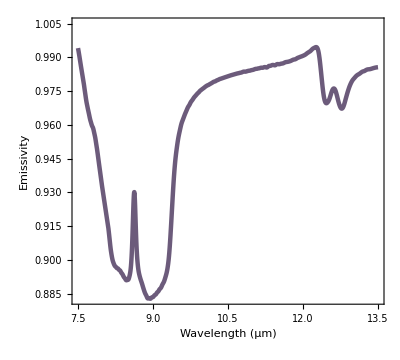

```mathematica
Plot[Interpolation[quartzDataNew,Method->"Spline"][x],{x,7.5,13.5},
PlotStyle->{RGBColor[{108,91,123}/255],Thickness[0.008]},
PlotRange->{All,{Automatic,1.005}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Emissivity",""},{"Wavelength (µm)","Quartz emissivity"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

```mathematica
planckData300=Table[{x 10^6,PlanckLawFunction[300,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
planckData290=Table[{x 10^6,PlanckLawFunction[290,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
planckData310=Table[{x 10^6,PlanckLawFunction[310,x]10^-6},{x,7.5 10^-6,13.5 10^-6,0.01 10^-6}];
tmp1={250,208,137}/255;
tmp2={255,156,91}/255;
tmp3={245,99,74}/255;
color1=RGBColor[tmp1];
color2=RGBColor[tmp2];
color3=RGBColor[tmp3];
```

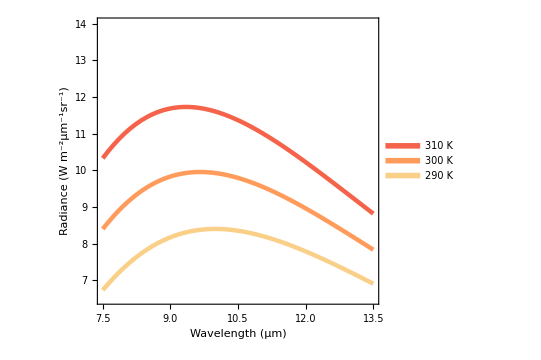

```mathematica
Plot[{Interpolation[planckData310][x],Interpolation[planckData300][x],Interpolation[planckData290][x]},{x,7.5,13.5},
(*PlotStyle->Directive[{{Red,Green,Blue},Thickness[0.01]}],*)
PlotStyle->{Directive[color3,Thickness[0.008]],Directive[color2,Thickness[0.008]],Directive[color1,Thickness[0.008]]},
PlotRange->{{Automatic,Automatic},{6.5,14.0}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
(*FrameTicks->{{#,1000000 #}&/@FindDivisions[{0.00002,.000002},20],{#, 0.000001#}&/@FindDivisions[{1000000,10000000},20]},*)
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Planck's law"}},
PlotLegends->Placed[LineLegend[{"310 K","300 K","290 K"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.76}],
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

```mathematica
quartzData=Import[NotebookDirectory[]<>"quartz.txt","Data"];
quartzData[[;;,1]]=quartzData[[;;,1]] 10^-6;
quartzData[[;;,2]]=1-quartzData[[;;,2]]/100;
eB290=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[290,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
eB300=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[300,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
eB310=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[310,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
```

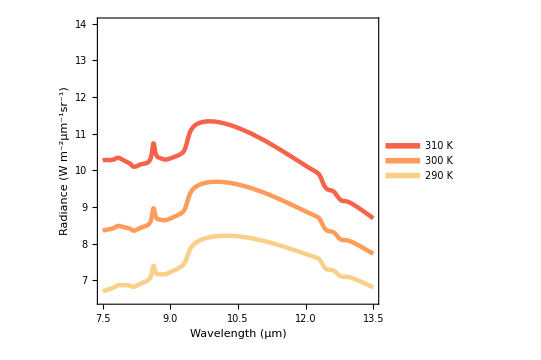

```mathematica
Plot[{Interpolation[eB310,Method->"Spline"][x],Interpolation[eB300,Method->"Spline"][x],Interpolation[eB290,Method->"Spline"][x]},{x,7.5,13.5},
PlotStyle->{Directive[color3,Thickness[0.008]],Directive[color2,Thickness[0.008]],Directive[color1,Thickness[0.008]]},
PlotRange->{All,{6.5,14}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Quartz radiance"}},
PlotLegends->Placed[LineLegend[{"310 K","300 K","290 K"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.76}],
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

## Chapter 1I

### TASI Response Functions

```mathematica
TASIBandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250} 10^-9;
```

```mathematica
TASIFWHM=109.5 10^-9;
```

```mathematica
tmpTASIdata=
Table[
Table[
{x 10^6,Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)]}
,{x,TASIBandCenters[[i]]-1.5475*10^-7,TASIBandCenters[[i]]+1.5475*10^-7,0.001 10^-6}]
,{i,1,32}];
```

```mathematica
TASIResponseFunction[bandn_,x_]:=Table[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{i,1,Length[TASIBandCenters]}][[bandn]]
```

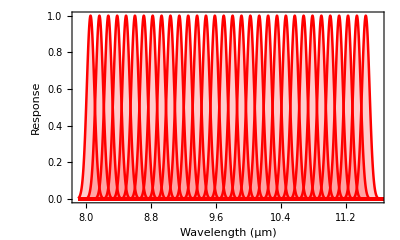

```mathematica
Show[
Table[
Plot[Exp[-(x 10^-6-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.9 ,11.7},
PlotRange->{{7.9,11.6},All},
PlotStyle->{TASIColor,Thickness[0.0045]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.20],TASIColor]
],{i,1,Length[TASIBandCenters]}],
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Response",""},{"Wavelength (µm)","TASI Response Functions"}},
AspectRatio->0.6,
ImageSize->{Automatic,180},
Frame->True,
FrameStyle->Black
]
```

### Quartz data and its plot

```mathematica
quartzData=Import[NotebookDirectory[]<>"quartz.txt","Data"];
quartzData[[;;,1]]=quartzData[[;;,1]] 10^-6;
quartzData[[;;,2]]=1-quartzData[[;;,2]]/100;
eB=Table[{quartzData[[x,1]]10^6,PlanckLawFunction[temp,quartzData[[x,1]]]quartzData[[x,2]]10^-6},{x,1,Length[quartzData[[;;,1]]]}];
```

```mathematica
data=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]PlanckLawFunction[temp,quartzData[[k,1]]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
data[[;;,1]]=data[[;;,1]] 10^6;
data[[;;,2]]=data[[;;,2]] 10^-6;
```

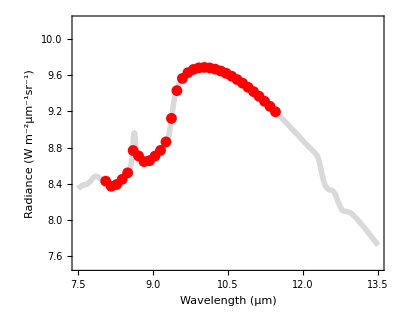

```mathematica
Show[
Plot[Interpolation[eB,Method->"Spline"][x],{x,7.5,13.5},
PlotStyle->{LightGray,Thickness[0.01]},PlotRange->{All,{7.5,10.2}}
],
ListPlot[data,PlotStyle->TASIColor,PlotRange->{All,{7.5,10.2}}],
PlotRange->{All,{7.5,10.2}},
ImageSize->{Automatic,180},
Frame->True,
AspectRatio->0.8,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Quartz radiance by TASI"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}}
]
```

### Data for radiometric calibrations, DN coeff computation and atmospheric correction

```mathematica
wavelengths=LmDataForComputationOfCalibCoef[[1,;;]]=Import[NotebookDirectory[]<>"dataForCalibProc/Lm/01_rad.txt","Data"][[;;,1]] 10^-9;

DNdataForComputationOfCalibCoef=ConstantArray[0,{2,32}];
tmpDNdataForComputationOfCalibCoef=Import[NotebookDirectory[]<>"dataForCalibProc/DN/01_DN.txt","Data"][[;;,2]];
DNdataForComputationOfCalibCoef[[1,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpDNdataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
tmpDNdataForComputationOfCalibCoef=Import[NotebookDirectory[]<>"dataForCalibProc/DN/02_DN.txt","Data"][[;;,2]];
DNdataForComputationOfCalibCoef[[2,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpDNdataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

LmDataForComputationOfCalibCoef=ConstantArray[0,{2,32}];
tmpLmDataForComputationOfCalibCoef=Import[NotebookDirectory[]<>"dataForCalibProc/Lm/01_rad.txt","Data"][[;;,2]]10^4;
LmDataForComputationOfCalibCoef[[1,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpLmDataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
tmpLmDataForComputationOfCalibCoef=Import[NotebookDirectory[]<>"dataForCalibProc/Lm/02_rad.txt","Data"][[;;,2]]10^4;
LmDataForComputationOfCalibCoef[[2,;;]]=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{wavelengths[[k]],tmpLmDataForComputationOfCalibCoef[[k]]},{k,1,60}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
calibCoef=Table[{c1,c2}/.NSolve[{DNdataForComputationOfCalibCoef[[1,i,2]]==c1+c2 LmDataForComputationOfCalibCoef[[1,i,2]],DNdataForComputationOfCalibCoef[[2,i,2]]==c1+c2 LmDataForComputationOfCalibCoef[[2,i,2]]},{c1,c2}][[1]],{i,1,Length[TASIBandCenters]}];
```

```mathematica
atmData=Import[NotebookDirectory[]<>"Brno_summer_day_low_altitude.tp8","Data"][[;;,3;;]];
transmissivity=atmData[[;;,1]];
upwelling=atmData[[;;,2]] 10^6;
downwelling=atmData[[;;,3]]10^6;
```

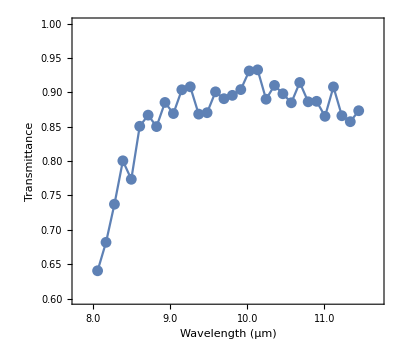

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,transmissivity[[i]]},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,transmissivity[[i]]},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{0.6,1}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Transmittance",SingleLetterItalics->False],""},{"Wavelength (µm)","Transmittance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

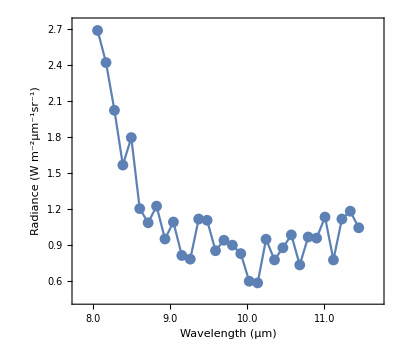

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,upwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,upwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{0.45,2.75}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Upwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

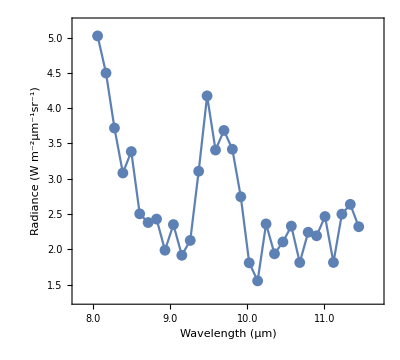

```mathematica
Show[
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}]],
ListPlot[Table[{TASIBandCenters[[i]] 10^6,downwelling[[i]]10^-6},{i,1,32}],Joined->True,PlotStyle->{Thickness[0.004]}],
PlotRange->{{7.8,11.7},{1.3,5.2}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Downwelling radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

```mathematica
quartzEmissivityByTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
Lq=Table[{TASIBandCenters[[i]],
quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]
},{i,1,Length[TASIBandCenters]}];
Lq[[;;,1]]=Lq[[;;,1]] 10^6;
Lq[[;;,2]]=Lq[[;;,2]] 10^-6;
```

```mathematica
Lm=Table[{TASIBandCenters[[i]],
transmissivity[[i]]quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]+transmissivity[[i]](1-quartzEmissivityByTASI[[i,2]])downwelling[[i]]+upwelling[[i]]
},{i,1,Length[TASIBandCenters]}];
Lm[[;;,1]]=Lm[[;;,1]] 10^6;
Lm[[;;,2]]=Lm[[;;,2]] 10^-6;
```

```mathematica
(*tmp=RGBColor[0,160/255,176/255]*)
(*tmp=RGBColor[1,0,0]*)
(*tmp=RGBColor[1,0.5,0]*)
(*tmp=RGBColor[143/255,190/255,0]*)
```

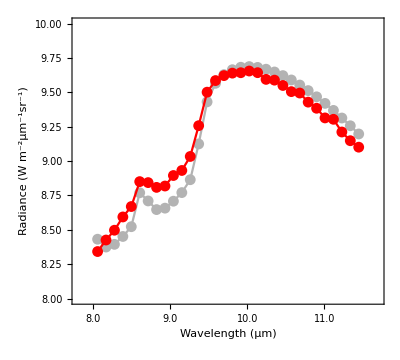

```mathematica
Show[
ListPlot[Lq,Joined->True,PlotStyle->{Thickness[0.004],RGBColor[0.7,0.7,0.7]}],
ListPlot[Lq,PlotStyle->RGBColor[0.7,0.7,0.7]],
ListPlot[Lm,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[Lm,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},{8,10}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","At-sensor radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
(*PlotLegends->Placed[LineLegend[{"At-sensor radiance","Quartz radiance"},LegendMarkerSize->8,LabelStyle->{FontSize->10,FontFamily->font}],{0.82,0.2}],*)
]
```

```mathematica
DN=Table[{TASIBandCenters[[i]],calibCoef[[i,1]]+calibCoef[[i,2]]Lm[[i,2]]},{i,1,Length[TASIBandCenters]}];
DN[[;;,1]]=DN[[;;,1]] 10^6;
```

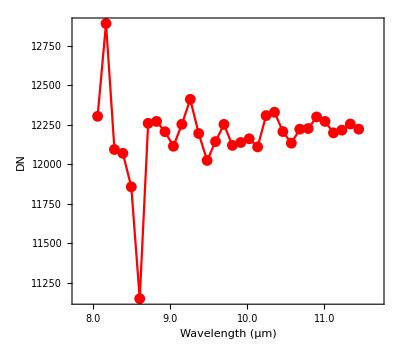

```mathematica
Show[
ListPlot[DN,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[DN,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},All},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["DN",SingleLetterItalics->False],""},{"Wavelength (µm)","Raw data"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

```mathematica
Lll=Table[{TASIBandCenters[[i]],
quartzEmissivityByTASI[[i,2]]PlanckLawFunction[temp,TASIBandCenters[[i]]]+(1-quartzEmissivityByTASI[[i,2]])downwelling[[i]]
},{i,1,Length[TASIBandCenters]}];
Lll[[;;,1]]=Lll[[;;,1]] 10^6;
Lll[[;;,2]]=Lll[[;;,2]] 10^-6;
```

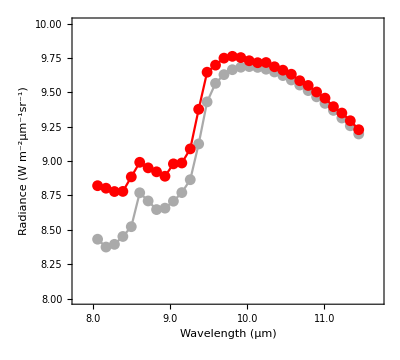

```mathematica
Show[
ListPlot[Lq,Joined->True,PlotStyle->{Thickness[0.004],Lighter[Gray]}],
ListPlot[Lq,PlotStyle->Lighter[Gray]],
ListPlot[Lll,Joined->True,PlotStyle->{Thickness[0.004],TASIColor}],
ListPlot[Lll,PlotStyle->TASIColor],
PlotRange->{{7.8,11.7},{8,10}},
ImageSize->{Automatic,180},
Frame->True,
Axes->False,
AspectRatio->0.9,
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{Style["Radiance (W m^-2µm^-1sr^-1)",SingleLetterItalics->False],""},{"Wavelength (µm)","Land-leaving radiance"}},
FrameStyle->{{{Black,Thickness[0.002]},{Black,Thickness[0.002]}},{{Black,Thickness[0.002]},{Black,Thickness[0.002]}}},
FrameTicks->{{Automatic,None},{{{8.0,"8.0"},{9.0,"9.0"},{10.0,"10.0"},{11.0,"11.0"}},None}}
]
```

## Chapter III

```mathematica
imageSize=200;
fontSize=11;
```

```mathematica
T=300;
```

### TASI Response Functions

```mathematica
TASIBandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250} 10^-9;
```

```mathematica
TASIFWHM=109.5 10^-9;
```

```mathematica
TASIResponseFunction[bandn_,x_]:=Table[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{i,1,Length[TASIBandCenters]}][[bandn]]
```

```mathematica
Show[
Table[
Plot[Exp[-(x 10^-6-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.9 ,11.7},
PlotRange->{{7.9,11.6},All},
PlotStyle->{TASIColor,Thickness[0.0045]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.20],TASIColor]
],{i,1,Length[TASIBandCenters]}],
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Response",""},{"Wavelength (µm)","TASI Response Functions"}},
AspectRatio->0.6,
ImageSize->{Automatic,180},
Frame->True,
FrameStyle->Black
]
```

-Graphics-

### Algorithms

#### Golden Section Search (1D optimization)

```mathematica
GoldenSectionSearch[fun_,l_,u_]:=
(
Module[{sol,n,dist,counter,emin,lastn},
n=30;
counter=1;
emin=ConstantArray[u,n];
sol=ConstantArray[0,{n,4,2}];
sol[[1,1,1]]=l;
sol[[1,1,2]]=fun[sol[[1,1,1]]][[1]];
sol[[1,4,1]]=u;
sol[[1,4,2]]=fun[sol[[1,4,1]]][[1]];
dist=sol[[1,4,1]]-sol[[1,1,1]];
sol[[1,2,1]]=sol[[1,1,1]]+dist(3-Sqrt[5])/2;
sol[[1,2,2]]=fun[sol[[1,2,1]]][[1]];
sol[[1,3,1]]=sol[[1,4,1]]-dist(3-Sqrt[5])/2;
sol[[1,3,2]]=fun[sol[[1,3,1]]][[1]];

Do[
If[sol[[counter-1,2,2]]<sol[[counter-1,3,2]],
sol[[counter,1,1]]=sol[[counter-1,1,1]];
sol[[counter,1,2]]=sol[[counter-1,1,2]];
sol[[counter,4,1]]=sol[[counter-1,3,1]];
sol[[counter,4,2]]=sol[[counter-1,3,2]];
sol[[counter,3,1]]=sol[[counter-1,2,1]];
sol[[counter,3,2]]=sol[[counter-1,2,2]];
sol[[counter,2,1]]=sol[[counter,1,1]]+sol[[counter,4,1]]-sol[[counter,3,1]];
sol[[counter,2,2]]=fun[sol[[counter,1,1]]+sol[[counter,4,1]]-sol[[counter,3,1]]][[1]];
,
sol[[counter,1,1]]=sol[[counter-1,2,1]];
sol[[counter,1,2]]=sol[[counter-1,2,2]];
sol[[counter,4,1]]=sol[[counter-1,4,1]];
sol[[counter,4,2]]=sol[[counter-1,4,2]];
sol[[counter,2,1]]=sol[[counter-1,3,1]];
sol[[counter,2,2]]=sol[[counter-1,3,2]];
sol[[counter,3,1]]=sol[[counter,1,1]]+sol[[counter,4,1]]-sol[[counter,2,1]];
sol[[counter,3,2]]=fun[sol[[counter,1,1]]+sol[[counter,4,1]]-sol[[counter,2,1]]][[1]];
];
emin[[counter]]=sol[[counter,Position[sol[[counter,;;,2]],Min[sol[[counter,;;,2]]]][[1,1]],1]];
(*If[Abs[emin[[counter-1]]-emin[[counter]]]<0.001,
lastn=counter;
Break[]];*)
lastn=counter;
,{counter,2,30}];
Return[{sol[[lastn,Position[sol[[lastn,;;,2]],Min[sol[[lastn,;;,2]]]][[1,1]],1]],sol}];
])
```

#### SBWTES

```mathematica
SBWTES[data_,Ldown_]:=
(
Module[{bT,BestT,tmpR,tmpT,s,weights,,wu,wl,sdata,minpos,maxpos,λ,dataforfit,fit,p1,p2,x,smoothedData,sbT,EstEmiss,EstEmiss2,tmprdata,MaxPos,emiss1D,emiss2D,c1,c2,const,ubound,BestT2,RatioMMD,approxFun,errf1D},

RatioMMD[emiss_]:=
(Module[{beta,MMD,emissmin,const1,const2,const3},
beta=Table[emiss[[i]]Length[emiss]/Total[emiss],{i,1,Length[emiss]}];
MMD=Max[beta]-Min[beta];
If[MMD<0.006,
Return[{emiss}]
,
const1=0.994;
const2=-0.687;
const3=0.737;
emissmin=const1+const2 (MMD^const3);
Return[{Table[beta[[i]]emissmin/Min[beta],{i,1,Length[emiss]}],MMD,emissmin}]]
]);

bT=Table[InversePlanckLawFunction[data[[j,2]],data[[j,1]],1],{j,1,Length[data]}];

(************************)
(*   1D   O P T I O N   *)
(************************)
approxFun[par1_,par2_,var_]:=(par1 var+par2);
(*approxFun[par1_,par2_,var_]:=1/(par1 var^3+par2);*)
(*approxFun[par1_,par2_,var_]:=par1 var^2+par2;*)
(*approxFun[par1_,par2_,var_]:= par1 Exp[1/var]+par2;*)

errf1D[l_]:=
(
const={c1,c2}/.FindFit[{{Min[bT],l},{Max[bT],1}},approxFun[c1,c2,x],{c1,c2},x];
emiss1D=Table[approxFun[const[[1]],const[[2]],x]/.x->bT[[i]],{i,1,Length[bT]}];
sdata=Table[{data[[i,1]],(data[[i,2]]-(1-emiss1D[[i]])Ldown[[i]])/emiss1D[[i]]},{i,1,Length[data]}];

tmpT=Max[Table[InversePlanckLawFunction[sdata[[i,2]],sdata[[i,1]],1],{i,1,Length[data]}]];
tmpR=Table[{data[[j,1]],PlanckLawFunction[tmpT,data[[j,1]]]},{j,1,Length[data]}];
Return[{Total[Abs[(tmpR[[;;,2]]/Norm[tmpR[[;;,2]],1])-(sdata[[;;,2]]/Norm[sdata[[;;,2]],1])]]}]
);

s={0,1};
s[[1]]=GoldenSectionSearch[errf1D,0.4,1][[1]];
tmpProc=GoldenSectionSearch[errf1D,0.4,1][[2]];
const={c1,c2}/.FindFit[{{Min[bT],s[[1]]},{Max[bT],s[[2]]}},approxFun[c1,c2,x],{c1,c2},x];
emiss1D=Table[approxFun[const[[1]],const[[2]],x]/.x->bT[[i]],{i,1,Length[bT]}];
sdata=Table[{data[[i,1]],(data[[i,2]]-(1-emiss1D[[i]])Ldown[[i]])/emiss1D[[i]]},{i,1,Length[data]}];

(*If[Variance[emiss1D]>1.7 10^-4,
s={0,0.96};
s[[1]]=GoldenSectionSearch[errf1D,0.4,0.96][[1]];
const={c1,c2}/.FindFit[{{Min[bT],s[[1]]},{Max[bT],s[[2]]}},approxFun[c1,c2,x],{c1,c2},x];
emiss1D=Table[approxFun[const[[1]],const[[2]],x]/.x->bT[[i]],{i,1,Length[bT]}];
sdata=Table[{data[[i,1]],(data[[i,2]]-(1-emiss1D[[i]])Ldown[[i]])/emiss1D[[i]]},{i,1,Length[data]}];
];*)

(**************************************************************)
(*                           T E S T                          *)
(**************************************************************)

(*tmpEmissMin=RatioMMD[emiss1D][[3]];
tmpEmissMinPosition=Position[emiss1D,Min[emiss1D]][[1,1]];
BestT=InversePlanckLawFunction[sdata[[tmpEmissMinPosition,2]],sdata[[tmpEmissMinPosition,1]],tmpEmissMin];*)

(*tmpEmissMin=RatioMMD[emiss1D][[3]];
tmpShift=Min[emiss1D]-tmpEmissMin;
emiss1D=emiss1D-tmpShift;
sdata=Table[{data[[i,1]],(data[[i,2]]-(1-emiss1D[[i]])Ldown[[i]])/emiss1D[[i]]},{i,1,Length[data]}];*)
BestT=Max[Table[InversePlanckLawFunction[sdata[[i,2]],sdata[[i,1]],1],{i,1,Length[data]}]];
EstEmiss=Table[(data[[i,2]]-Ldown[[i]])/(PlanckLawFunction[BestT,data[[i,1]]]-Ldown[[i]]),{i,1,Length[data]}];

(**************************************************************)
(*   S B W   T e m p   &    E m i s   E S T I M A T I O N   *)
(**************************************************************)

BestT=Max[Table[InversePlanckLawFunction[sdata[[i,2]],sdata[[i,1]],1],{i,1,Length[data]}]];
EstEmiss=Table[(data[[i,2]]-Ldown[[i]])/(PlanckLawFunction[BestT,data[[i,1]]]-Ldown[[i]]),{i,1,Length[data]}];

(**************************************************************)
(*   T E S   T e m p   &    E m i s   E S T I M A T I O N   *)
(**************************************************************)

EstEmiss2=RatioMMD[EstEmiss][[1]];
MaxPos=Position[EstEmiss2,Max[EstEmiss2]][[1,1]];
BestT2=InversePlanckLawFunction[(data[[MaxPos,2]]-(1-EstEmiss2[[MaxPos]])Ldown[[MaxPos]]),data[[MaxPos,1]],EstEmiss2[[MaxPos]]];

EstEmiss2=Table[(data[[i,2]]-Ldown[[i]])/(PlanckLawFunction[BestT2,data[[i,1]]]-Ldown[[i]]),{i,1,Length[data]}];

Return[{BestT2,EstEmiss2,BestT,EstEmiss,const,bT,s,emiss1D,tmpProc}];
]
)
```

### Mid-ladtitude atmosphere loading

```mathematica
atmDataSatellite=Import[NotebookDirectory[]<>"midLatitudeSummerAtm/Mid_Latitude_Summer_test_SATELLITE.tp8","Data"][[2;;,1;;]];
standardSatelliteAtmWavelength=atmDataSatellite[[;;,1]]10^-6;
standardSatelliteAtmTrans=atmDataSatellite[[;;,2]];
standardSatelliteAtmLup=atmDataSatellite[[;;,3]]10^6;
standardSatelliteAtmLdown=atmDataSatellite[[;;,4]]10^6;
standardSatelliteAtmLdownSun=atmDataSatellite[[;;,5]]10^6;
```

```mathematica
standardSatelliteAtmLdownSunASTER=Table[NIntegrate[Interpolation[Table[{standardSatelliteAtmWavelength[[k]],standardSatelliteAtmLdownSun[[k]]},{k,1,Length[standardSatelliteAtmWavelength]}]][λ]ASTERResponseFunction[j,λ],{λ,ASTERxmin,ASTERxmax}]/NIntegrate[ASTERResponseFunction[j,λ],{λ,ASTERxmin,ASTERxmax}],{j,1,Length[ASTERBandCenters]}];
```

```mathematica
atmDataAircraft=Import[NotebookDirectory[]<>"midLatitudeSummerAtm/Mid_Latitude_Summer_test_AIRCRAFT.tp8","Data"][[2;;,1;;]];
standardAircraftAtmWavelength=atmDataAircraft[[;;,1]]10^-6;
standardAircraftAtmTrans=atmDataAircraft[[;;,2]];
standardAircraftAtmLup=atmDataAircraft[[;;,3]]10^6;
standardAircraftAtmLdown=atmDataAircraft[[;;,4]]10^6;
standardAircraftAtmLdownSun=atmDataAircraft[[;;,5]]10^6;
```

```mathematica
standardAircraftAtmLdownSunTASI=Table[NIntegrate[Interpolation[Table[{standardAircraftAtmWavelength[[k]],standardAircraftAtmLdownSun[[k]]},{k,1,Length[standardAircraftAtmWavelength]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}],{j,1,Length[TASIBandCenters]}];
```

```mathematica
standardAircraftAtmLdownSunAHS=Table[NIntegrate[Interpolation[Table[{standardAircraftAtmWavelength[[k]],standardAircraftAtmLdownSun[[k]]},{k,1,Length[standardAircraftAtmWavelength]}]][λ]AHSResponseFunction[j,λ],{λ,Min[AHSResponseFunctionsData[[j,;;,1]]],Max[AHSResponseFunctionsData[[j,;;,1]]]},Method->"LocalAdaptive"]/NIntegrate[AHSResponseFunction[j,λ],{λ,Min[AHSResponseFunctionsData[[j,;;,1]]],Max[AHSResponseFunctionsData[[j,;;,1]]]},Method->"LocalAdaptive"],{j,1,Length[AHSBandCenters]}];
```

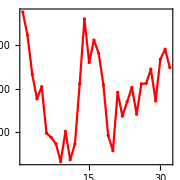
-Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[{{
Show[
ListPlot[standardAircraftAtmLdownSunTASI,PlotStyle->TASIColor,Joined->True],
ListPlot[standardAircraftAtmLdownSunTASI,PlotStyle->TASIColor],
PlotRange->All,ImageSize->180,Frame->True,AspectRatio->1,LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},FrameStyle->Black],
Show[
ListPlot[standardAircraftAtmLdownSunAHS,PlotStyle->AHSColor,Joined->True],
ListPlot[standardAircraftAtmLdownSunAHS,PlotStyle->AHSColor],
PlotRange->All,ImageSize->180,Frame->True,AspectRatio->1,LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},FrameStyle->Black],
Show[
ListPlot[standardSatelliteAtmLdownSunASTER,PlotStyle->ASTERColor,Joined->True],
ListPlot[standardSatelliteAtmLdownSunASTER,PlotStyle->ASTERColor],
PlotRange->All,ImageSize->180,Frame->True,AspectRatio->1,LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},FrameStyle->Black]
}}]
```

### 01 - Green Grass

```mathematica
waterData=Import[NotebookDirectory[]<>"sampleEmissivities/Grass.txt","Data"];
waterData[[;;,1]]=waterData[[;;,1]]10^-6;
waterData[[;;,2]]=1-waterData[[;;,2]]/100;
```

#### TASI

```mathematica
waterDataTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{waterData[[m,1]],waterData[[m,2]]PlanckLawFunction[T,waterData[[m,1]]]},{m,1,Length[waterData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

waterEmissTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{waterData[[k,1]],waterData[[k,2]]},{k,1,Length[waterData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

waterTASIbTvsEmis=Table[{InversePlanckLawFunction[waterDataTASI[[i,2]],waterDataTASI[[i,1]],1],waterEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];

waterConstTASI=SBWTES[waterDataTASI,ConstantArray[0,Length[TASIBandCenters]]][[5]];
```

```mathematica
waterDataTASILll=Table[{TASIBandCenters[[j]],waterDataTASI[[j,2]]+(1-waterEmissTASI[[j,2]])standardAircraftAtmLdownSunTASI[[j]]},{j,1,Length[TASIBandCenters]}];
waterTASIbTvsEmisLll=Table[{InversePlanckLawFunction[waterDataTASILll[[i,2]],waterDataTASI[[i,1]],1],waterEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];
waterConstTASILll=SBWTES[waterDataTASILll,standardAircraftAtmLdownSunTASI][[5]];
```

```mathematica
waterDataToPlot=waterData ;
waterDataToPlot[[;;,1]]=waterDataToPlot[[;;,1]] 10^6;

waterEmissTASIToPlot=waterEmissTASI;
waterEmissTASIToPlot[[;;,1]]=waterEmissTASIToPlot[[;;,1]] 10^6;
```

```mathematica
waterTASIbTToPlot=Quiet[Table[{waterEmissTASIToPlot[[i,1]],Interpolation[{{Min[waterTASIbTvsEmisLll[[;;,1]]]+1,Min[waterEmissTASIToPlot[[;;,2]]]},{Max[waterTASIbTvsEmisLll[[;;,1]]]+1,Max[waterEmissTASIToPlot[[;;,2]]]}}][waterTASIbTvsEmisLll[[i,1]]]},{i,1,Length[TASIBandCenters]}]];
```

#### Plot

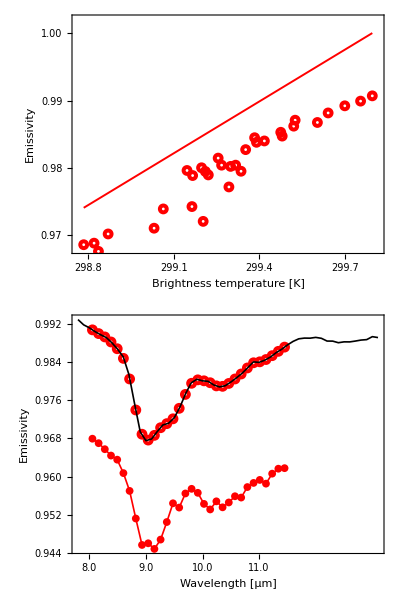

```mathematica
padding={{41,48},{35,22}};
Grid[{
{
Show[
ListPlot[waterTASIbTvsEmisLll,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[waterAHSbTvsEmisLll,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],
ListPlot[waterASTERbTvsEmisLll,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)

Plot[approxFun[waterConstTASILll[[1]],waterConstTASILll[[2]],x],{x,Min[waterTASIbTvsEmisLll[[;;,1]]],Max[waterTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{TASIColor,Thickness[0.007]}],
(*Plot[approxFun[waterConstAHSLll[[1]],waterConstAHSLll[[2]],x],{x,Min[waterAHSbTvsEmisLll[[;;,1]]],Max[waterTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{AHSColor,Dashing[Large],Thickness[lineThickness]}],
Plot[approxFun[waterConstASTERLll[[1]],waterConstASTERLll[[2]],x],{x,Min[waterAHSbTvsEmisLll[[;;,1]]],Max[waterTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{ASTERColor,Dashing[{0,0.02}],Thickness[lineThickness]}],*)

PlotRange->{{Min[waterTASIbTvsEmisLll[[;;,1]]]-0.02,Max[waterTASIbTvsEmisLll[[;;,1]]]+0.02},{0.968,1.002}},
ImageSize->imageSize,
Frame->True,
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Emissivity",""},{"Brightness temperature [K]"(*Subscript["T","b"]*),"Green Grass"}},
FrameStyle->Black,
Axes->{False, False},
FrameTicks->{{{{0.97,"0.97"},{0.98,"0.98"},{0.99,"0.99"},{1.00,"1.00"}},Automatic},{{298.8,299.1,299.4,299.7},Automatic}},
ImagePadding->padding
]
},
{
Show[
ListPlot[waterEmissTASIToPlot,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[waterEmissASTERToPlot,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)
(*ListPlot[waterEmissAHSToPlot,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],*)

ListPlot[waterDataToPlot[[9;;62,;;]],
PlotStyle->{Black,Thickness[0.006]},
Joined->True
],

ListPlot[waterTASIbTToPlot,PlotStyle->{TASIColor,Thickness[0.006]},PlotMarkers->{"•",8},Joined->True],
(*ListPlot[waterAHSbTToPlot,PlotStyle->AHSColor,PlotMarkers->{"■",28},Joined->True],*)
(*ListPlot[waterASTERbTToPlot,PlotStyle->ASTERColor,PlotMarkers->{"▲", 28},Joined->True],*)

PlotRange->{{8,11.5},{Automatic,1}},
ImageSize->imageSize,
Frame->True,
Axes->False,
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Emissivity","Brightness temperature [K]"},{"Wavelength [µm]"(*Subscript["T","b"]*),"Green Grass"}},
FrameStyle->Black,
FrameTicks->{{Automatic,{{0.9541934828197747,"298.8"},{0.9614813350187569,"299.1"},{0.9687691872177376,"299.4"},{0.9760570394167198,"299.7"},{0.983344891615702,"300.0"},{0.9906327438146842,"300.3"},{0.9979205960136664,"300.6"}}},{{{8,"8.0"},{9,"9.0"},{10,"10.0"},{11,"11.0"}},Automatic}},
ImagePadding->padding
]
}
}]
```

### 02 - Fine Sandy Loam

```mathematica
limestoneData=Import[NotebookDirectory[]<>"sampleEmissivities/MMD_15.txt","Data"];
limestoneData[[;;,1]]=limestoneData[[;;,1]]10^-6;
limestoneData[[;;,2]]=1-limestoneData[[;;,2]]/100;
```

#### TASI

```mathematica
T=300;
```

```mathematica
limestoneDataTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{limestoneData[[k,1]],limestoneData[[k,2]]PlanckLawFunction[T,limestoneData[[k,1]]]},{k,1,Length[limestoneData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

limestoneEmissTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{limestoneData[[k,1]],limestoneData[[k,2]]},{k,1,Length[limestoneData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];

limestoneTASIbTvsEmis=Table[{InversePlanckLawFunction[limestoneDataTASI[[i,2]],limestoneDataTASI[[i,1]],1],limestoneEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];

limestoneConstTASI=SBWTES[limestoneDataTASI,ConstantArray[0,Length[TASIBandCenters]]][[5]];
```

```mathematica
limestoneDataTASILll=Table[{TASIBandCenters[[j]],limestoneDataTASI[[j,2]]+(1-limestoneEmissTASI[[j,2]])standardAircraftAtmLdownSunTASI[[j]]},{j,1,Length[TASIBandCenters]}];
limestoneTASIbTvsEmisLll=Table[{InversePlanckLawFunction[limestoneDataTASILll[[i,2]],limestoneDataTASI[[i,1]],1],limestoneEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];
limestoneConstTASILll=SBWTES[limestoneDataTASILll,standardAircraftAtmLdownSunTASI][[5]];
```

```mathematica
limestoneDataToPlot=limestoneData ;
limestoneDataToPlot[[;;,1]]=limestoneDataToPlot[[;;,1]] 10^6;

limestoneEmissTASIToPlot=limestoneEmissTASI;
limestoneEmissTASIToPlot[[;;,1]]=limestoneEmissTASIToPlot[[;;,1]] 10^6;
```

```mathematica
limestoneTASIbTToPlot=Quiet[Table[{limestoneEmissTASIToPlot[[i,1]],Interpolation[{{Min[limestoneTASIbTvsEmisLll[[;;,1]]]+2,Min[limestoneEmissTASIToPlot[[;;,2]]]},{Max[limestoneTASIbTvsEmisLll[[;;,1]]]+2,Max[limestoneEmissTASIToPlot[[;;,2]]]}}][limestoneTASIbTvsEmisLll[[i,1]]]},{i,1,Length[TASIBandCenters]}]];
```

#### Plot

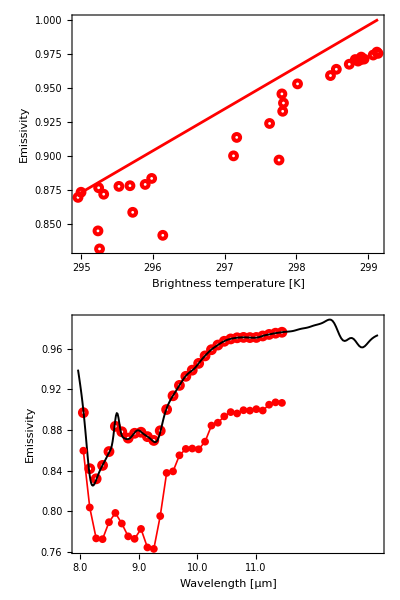

```mathematica
padding={{41,48},{35,22}};
Grid[{
{
Show[
ListPlot[limestoneTASIbTvsEmisLll,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[limestoneAHSbTvsEmisLll,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],
ListPlot[limestoneASTERbTvsEmisLll,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)

Plot[approxFun[limestoneConstTASILll[[1]],limestoneConstTASILll[[2]],x],{x,Min[limestoneTASIbTvsEmisLll[[;;,1]]],Max[limestoneTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{TASIColor,Thickness[lineThickness]}],
(*Plot[approxFun[limestoneConstAHSLll[[1]],limestoneConstAHSLll[[2]],x],{x,Min[limestoneTASIbTvsEmisLll[[;;,1]]],Max[limestoneTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{AHSColor,Dashing[Large],Thickness[lineThickness]}],
Plot[approxFun[limestoneConstASTERLll[[1]],limestoneConstASTERLll[[2]],x],{x,Min[limestoneTASIbTvsEmisLll[[;;,1]]],Max[limestoneTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{ASTERColor,Dashing[{0,0.02}],Thickness[lineThickness]}],*)

PlotRange->{All,{Automatic,1}},
ImageSize->imageSize,
Frame->True,
Axes->{False,False},
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Emissivity",""},{"Brightness temperature [K]"(*Subscript["T","b"]*),"Fine Sandy Loam"}},
FrameStyle->Black,
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding
]
},
{Show[
ListPlot[limestoneEmissTASIToPlot,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[limestoneEmissASTERToPlot,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)
(*ListPlot[limestoneEmissAHSToPlot,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],*)

ListPlot[limestoneDataToPlot[[90;;345,;;]],
PlotStyle->{Black,Thickness[0.007]},
Joined->True
],

ListPlot[limestoneTASIbTToPlot,PlotStyle->{TASIColor,Thickness[0.006]},PlotMarkers->{"•",8},Joined->True],
(*ListPlot[limestoneAHSbTToPlot,PlotStyle->AHSColor,PlotMarkers->{"■",28},Joined->True],*)
(*ListPlot[limestoneASTERbTToPlot,PlotStyle->ASTERColor,PlotMarkers->{"▲", 28},Joined->True],*)

PlotRange->{{8,11.5},{Automatic,1}},
ImageSize->imageSize,
Frame->True,
Axes->False,
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Emissivity","Brightness temperature [K]"},{"Wavelength [µm]"(*Subscript["T","b"]*),"Fine Sandy Loam"}},
FrameStyle->Black,
FrameTicks->{{Automatic,Quiet[Table[{Interpolation[{{Min[limestoneTASIbTvsEmisLll[[;;,1]]]+3.3,Min[limestoneEmissTASIToPlot[[;;,2]]]},{Max[limestoneTASIbTvsEmisLll[[;;,1]]]+3.3,Max[limestoneEmissTASIToPlot[[;;,2]]]}}][i],ToString[i]},{i,295,303,2}]]},{{{8,"8.0"},{9,"9.0"},{10,"10.0"},{11,"11.0"}},Automatic}},
ImagePadding->padding
]}
}]
```

### 03 - Altered Volcanic Tuff

```mathematica
quartzData=Import[NotebookDirectory[]<>"sampleEmissivities/MMD_25.txt","Data"];
quartzData[[;;,1]]=quartzData[[;;,1]]10^-6;
quartzData[[;;,2]]=1-quartzData[[;;,2]]/100;
```

#### TASI

```mathematica
T=300;
```

```mathematica
quartzDataTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]PlanckLawFunction[T,quartzData[[k,1]]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
quartzEmissTASI=Table[{TASIBandCenters[[j]],NIntegrate[Interpolation[Table[{quartzData[[k,1]],quartzData[[k,2]]},{k,1,Length[quartzData]}]][λ]TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]/NIntegrate[TASIResponseFunction[j,λ],{λ,7.1 10^-6,12 10^-6}]},{j,1,Length[TASIBandCenters]}];
```

```mathematica
quartzTASIbTvsEmis=Table[{InversePlanckLawFunction[quartzDataTASI[[i,2]],quartzDataTASI[[i,1]],1],quartzEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];
```

```mathematica
quartzConstTASI=SBWTES[quartzDataTASI,ConstantArray[0,Length[TASIBandCenters]]][[5]];
```

```mathematica
quartzDataTASILll=Table[{TASIBandCenters[[j]],quartzDataTASI[[j,2]]+(1-quartzEmissTASI[[j,2]])standardAircraftAtmLdownSunTASI[[j]]},{j,1,Length[TASIBandCenters]}];
quartzTASIbTvsEmisLll=Table[{InversePlanckLawFunction[quartzDataTASILll[[i,2]],quartzDataTASI[[i,1]],1],quartzEmissTASI[[i,2]]},{i,1,Length[TASIBandCenters]}];
quartzConstTASILll=SBWTES[quartzDataTASILll,standardAircraftAtmLdownSunTASI][[5]];
```

```mathematica
quartzDataToPlot=quartzData ;
quartzDataToPlot[[;;,1]]=quartzDataToPlot[[;;,1]] 10^6;

quartzEmissTASIToPlot=quartzEmissTASI;
quartzEmissTASIToPlot[[;;,1]]=quartzEmissTASIToPlot[[;;,1]] 10^6;

quartzTASIbTToPlot=Quiet[Table[{quartzEmissTASIToPlot[[i,1]],Interpolation[{{Min[quartzTASIbTvsEmisLll[[;;,1]]]+5,Min[quartzEmissTASIToPlot[[;;,2]]]},{Max[quartzTASIbTvsEmisLll[[;;,1]]]+5,Max[quartzEmissTASIToPlot[[;;,2]]]}}][quartzTASIbTvsEmisLll[[i,1]]]},{i,1,Length[TASIBandCenters]}]];
```

#### Plot

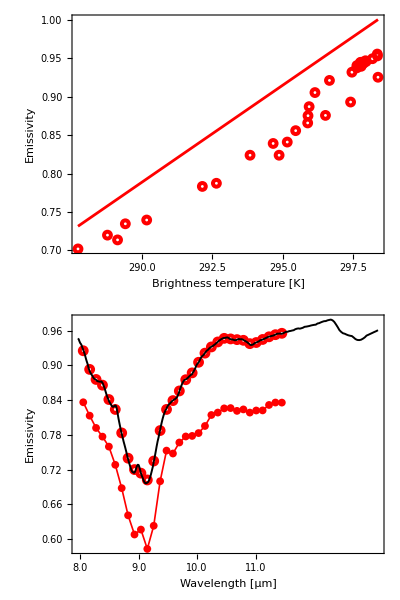

```mathematica
padding={{41,48},{35,22}};
Grid[{
{
Show[
ListPlot[quartzTASIbTvsEmisLll,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[quartzAHSbTvsEmisLll,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],
ListPlot[quartzASTERbTvsEmisLll,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)

Plot[approxFun[quartzConstTASILll[[1]],quartzConstTASILll[[2]],x],{x,Min[quartzTASIbTvsEmisLll[[;;,1]]],Max[quartzTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{TASIColor,Thickness[lineThickness]}],
(*Plot[approxFun[quartzConstAHSLll[[1]],quartzConstAHSLll[[2]],x],{x,Min[quartzTASIbTvsEmisLll[[;;,1]]],Max[quartzTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{AHSColor,Thickness[lineThickness],Dashing[Large]}],
Plot[approxFun[quartzConstASTERLll[[1]],quartzConstASTERLll[[2]],x],{x,Min[quartzTASIbTvsEmisLll[[;;,1]]],Max[quartzTASIbTvsEmisLll[[;;,1]]]},PlotStyle->{ASTERColor,Dashing[{0,0.02}],Thickness[lineThickness]}],*)

PlotRange->{All,{Automatic,1}},
ImageSize->imageSize,
Frame->True,
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
Axes->False,FrameLabel->{{"Emissivity",""},{"Brightness temperature [K]"(*Subscript["T","b"]*),"Altered Volcanic Tuff"}},
FrameStyle->Black,
ImagePadding->padding
]
},{
Show[
ListPlot[quartzEmissTASIToPlot,PlotStyle->TASIColor,PlotMarkers->Graphics[{Thickness[0.25],Circle[]},ImageSize->4]],
(*ListPlot[quartzEmissASTERToPlot,PlotStyle->ASTERColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],ASTERColor}],FaceForm[],Triangle[{{-1,-1},{0,2Sqrt[3]/3},{1,-1}}]},ImageSize->15]],*)
(*ListPlot[quartzEmissAHSToPlot,PlotStyle->AHSColor,PlotMarkers->Graphics[{EdgeForm[{Thickness[0.25],AHSColor}],FaceForm[],Rectangle[{1,1},{-1,-1}]},ImageSize->15]],*)

ListPlot[quartzDataToPlot[[90;;345,;;]],
PlotStyle->{Black,Thickness[0.007]},
Joined->True
],

ListPlot[quartzTASIbTToPlot,PlotStyle->{TASIColor,Thickness[0.006]},PlotMarkers->{"•",8},Joined->True],
(*ListPlot[quartzAHSbTToPlot,PlotStyle->AHSColor,PlotMarkers->{"■",28},Joined->True],*)
(*ListPlot[quartzASTERbTToPlot,PlotStyle->ASTERColor,PlotMarkers->{"▲", 28},Joined->True],*)

PlotRange->{{8,11.5},{Automatic,1}},
ImageSize->imageSize,
Frame->True,
Axes->False,
AspectRatio->1,
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Emissivity","Brightness temperature [K]"},{"Wavelength [µm]","Altered Volcanic Tuff"}},
FrameStyle->Black,
FrameTicks->{{Automatic,Quiet[Table[
{Interpolation[{{Min[quartzTASIbTvsEmisLll[[;;,1]]]+5,Min[quartzEmissTASIToPlot[[;;,2]]]},{Max[quartzTASIbTvsEmisLll[[;;,1]]]+5,Max[quartzEmissTASIToPlot[[;;,2]]]}}][i],ToString[i]}
,{i,{288,291,294,297,300,303,306}}]]},{{{8,"8.0"},{9,"9.0"},{10,"10.0"},{11,"11.0"}},Automatic}},
ImagePadding->padding
]
}
}]
```

## Chapter IV

### TASI Response Functions

```mathematica
TASIBandCenters={8054.750,8164.250,8273.750,8383.250,8492.750,8602.250,8711.750,8821.250,8930.750,9040.250,9149.750,9259.250,9368.750,9478.250,9587.750,9697.250,9806.750,9916.250,10025.750,10135.250,10244.750,10354.250,10463.750,10573.250,10682.750,10792.250,10901.750,11011.250,11120.750,11230.250,11339.750,11449.250} 10^-9;
```

```mathematica
TASIFWHM=109.5 10^-9;
```

```mathematica
TASIResponseFunction[bandn_,x_]:=Table[Exp[-(x-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{i,1,Length[TASIBandCenters]}][[bandn]]
```

```mathematica
Show[
Table[
Plot[Exp[-(x 10^-6-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.9 ,11.7},
PlotRange->{{7.9,11.6},All},
PlotStyle->{TASIColor,Thickness[0.0045]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.20],TASIColor]
],{i,1,Length[TASIBandCenters]}],
LabelStyle->{FontSize->12,FontFamily->font,Black},
FrameLabel->{{"Response",""},{"Wavelength (µm)","TASI Response Functions"}},
AspectRatio->0.6,
ImageSize->{Automatic,180},
Frame->True,
FrameStyle->Black
]
```

-Graphics-

### AHS Response Functions

```mathematica
AHSResponseFunction1Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_71.txt","Data"];
AHSResponseFunction2Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_72.txt","Data"];
AHSResponseFunction3Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_73.txt","Data"];
AHSResponseFunction4Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_74.txt","Data"];
AHSResponseFunction5Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_75.txt","Data"];
AHSResponseFunction6Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_76.txt","Data"];
AHSResponseFunction7Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_77.txt","Data"];
AHSResponseFunction8Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_78.txt","Data"];
AHSResponseFunction9Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_79.txt","Data"];
AHSResponseFunction10Data=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/AHS/AHS Response Functions/AHS_band_80.txt","Data"];
```

```mathematica
(*AHSResponseFunction1Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_71.txt","Data"];
AHSResponseFunction2Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_72.txt","Data"];
AHSResponseFunction3Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_73.txt","Data"];
AHSResponseFunction4Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_74.txt","Data"];
AHSResponseFunction5Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_75.txt","Data"];
AHSResponseFunction6Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_76.txt","Data"];
AHSResponseFunction7Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_77.txt","Data"];
AHSResponseFunction8Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_78.txt","Data"];
AHSResponseFunction9Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_79.txt","Data"];
AHSResponseFunction10Data=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\AHS\\AHS Response Functions\\AHS_band_80.txt","Data"];*)
```

```mathematica
AHSResponseFunction1Data[[;;,1]]=AHSResponseFunction1Data[[;;,1]]10^-6;
AHSResponseFunction2Data[[;;,1]]=AHSResponseFunction2Data[[;;,1]]10^-6;
AHSResponseFunction3Data[[;;,1]]=AHSResponseFunction3Data[[;;,1]]10^-6;
AHSResponseFunction4Data[[;;,1]]=AHSResponseFunction4Data[[;;,1]]10^-6;
AHSResponseFunction5Data[[;;,1]]=AHSResponseFunction5Data[[;;,1]]10^-6;
AHSResponseFunction6Data[[;;,1]]=AHSResponseFunction6Data[[;;,1]]10^-6;
AHSResponseFunction7Data[[;;,1]]=AHSResponseFunction7Data[[;;,1]]10^-6;
AHSResponseFunction8Data[[;;,1]]=AHSResponseFunction8Data[[;;,1]]10^-6;
AHSResponseFunction9Data[[;;,1]]=AHSResponseFunction9Data[[;;,1]]10^-6;
AHSResponseFunction10Data[[;;,1]]=AHSResponseFunction10Data[[;;,1]]10^-6;
```

```mathematica
AHSResponseFunctionsData={AHSResponseFunction1Data,AHSResponseFunction2Data,AHSResponseFunction3Data,AHSResponseFunction4Data,AHSResponseFunction5Data,AHSResponseFunction6Data,AHSResponseFunction7Data,AHSResponseFunction8Data,AHSResponseFunction9Data,AHSResponseFunction10Data};
```

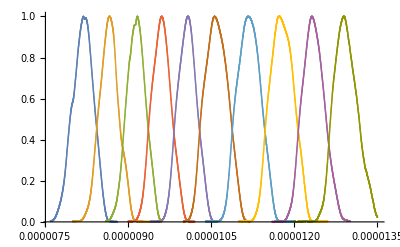

```mathematica
ListPlot[{AHSResponseFunction1Data,AHSResponseFunction2Data,AHSResponseFunction3Data,AHSResponseFunction4Data,AHSResponseFunction5Data,AHSResponseFunction6Data,AHSResponseFunction7Data,AHSResponseFunction8Data,AHSResponseFunction9Data,AHSResponseFunction10Data},PlotRange->All]
```

```mathematica
AHSBandCenters={8.192,8.66,9.166,9.605,10.077,10.556,11.164,11.716,12.317,12.889} 10^-6;
```

```mathematica
AHSResponseFunction[bandn_,x_]:=Interpolation[AHSResponseFunctionsData[[bandn]]][x]
```

### ASTER Response Functions

```mathematica
ASTERResponseFunctionsData=Import["C:\\Users\\Marek\\Dropbox\\CSAV\\GCU\\MLETES\\ASTER\\ASTER response functions\\ASTER_ResponseFunction.txt","Table"][[5;;,;;]];
ASTERResponseFunctionsData=Import["/Users/Marek/Dropbox/CSAV/GCU/MLETES/ASTER/ASTER response functions/ASTER_ResponseFunction.txt","Table"][[5;;,;;]];
For[i=1,i≤Dimensions[ASTERResponseFunctionsData][[1]],i++,
For[j=1,j<=Dimensions[ASTERResponseFunctionsData][[2]],j+=2,
ASTERResponseFunctionsData[[i,j]]=ASTERResponseFunctionsData[[i,j]]10^-6;
]
]
ASTERband1=ASTERResponseFunctionsData[[;;,1;;2]];
ASTERband2=ASTERResponseFunctionsData[[;;,3;;4]];
ASTERband3=ASTERResponseFunctionsData[[;;,5;;6]];
ASTERband4=ASTERResponseFunctionsData[[;;,7;;8]];
ASTERband5=ASTERResponseFunctionsData[[;;,9;;10]];
ASTERBandCenters={8.29,8.635,9.079,10.659,11.29} 10^-6;;
```

Import::nffil: File not found during Import.

Part::take: Cannot take positions 5 through -1 in $Failed.

```mathematica
ASTERxmin=N[Min[ASTERResponseFunctionsData[[;;,1]]]];
ASTERxmax=N[Max[ASTERResponseFunctionsData[[;;,1]]]];
```

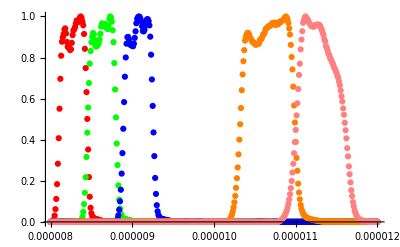

```mathematica
Show[
ListPlot[ASTERband1,PlotRange->All,PlotStyle->Red],
ListPlot[ASTERband2,PlotRange->All,PlotStyle->Green],
ListPlot[ASTERband3,PlotRange->All,PlotStyle->Blue],
ListPlot[ASTERband4,PlotRange->All,PlotStyle->Orange],
ListPlot[ASTERband5,PlotRange->All,PlotStyle->Pink],
PlotRange->All]
```

```mathematica
ASTERResponseFunction[bandn_,x_]:=Interpolation[ASTERResponseFunctionsData[[;;,2bandn-1;;2bandn]]][x]
```

### Plot all response functions

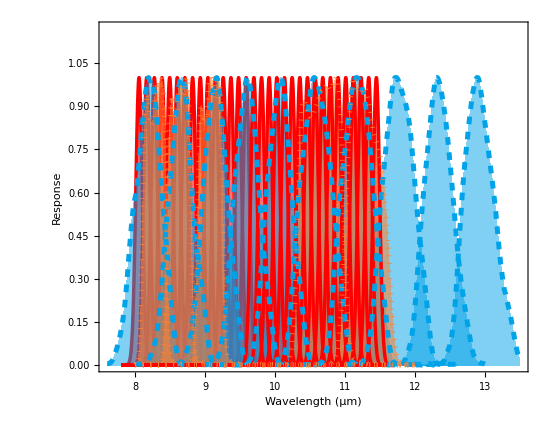
-Graphics- |

```mathematica
TableForm[{
{Show[

Table[
Plot[Exp[-(x 10^-6-TASIBandCenters[[i]])^2/(2(TASIFWHM/(2Sqrt[2Log[2]]))^2)],{x,7.8 ,11.6},
PlotRange->{All,{Automatic,1.17}},
PlotStyle->{TASIColor,Thickness[0.0045]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.55],TASIColor]
],{i,1,Length[TASIBandCenters]}],

Table[
Plot[AHSResponseFunction[i,x 10^-6],{x,Min[AHSResponseFunctionsData[[i,;;,1]]]10^6,Max[AHSResponseFunctionsData[[i,;;,1]]]10^6},
PlotRange->{All,{Automatic,1.17}},
PlotStyle->{AHSColor,Dashing[{0.01,0.01}],Thickness[0.0065]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.5],AHSColor]
],{i,1,Length[AHSBandCenters]}],

Table[
Plot[ASTERResponseFunction[i,x 10^-6],{x,ASTERxmin 10^6,ASTERxmax 10^6},
PlotRange->{All,{Automatic,1.17}},
PlotStyle->{ASTERColor,Dashing[{0.001,0.009}],Thickness[0.0065]},
Filling->Bottom,
FillingStyle->Directive[Opacity[0.55],ASTERColor]
],{i,1,Length[ASTERBandCenters]}],

LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
FrameLabel->{{"Response",""},{"Wavelength (µm)","Response Functions"}},
FrameTicks->{{Automatic,Automatic},{Automatic,{{8.2,"10"},{8.7,"11"},{9.2,"12"},{10.66,"13"},{11.29,"14"}}}},
AspectRatio->0.8,
ImageSize->550,
Frame->True,
FrameStyle->Black
],
LineLegend[{ASTERColor,AHSColor,TASIColor},{"ASTER","AHS","TASI"},
LabelStyle->{FontSize->fontSize,FontFamily->font,Black},
LegendMargins->0
]}
},TableSpacing->{0, 0}]
```

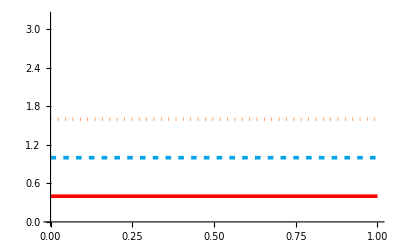

```mathematica
Show[
Plot[1.6,{x,0,1},PlotStyle->{ASTERColor,Dashing[{0.001,0.012}],Thickness[0.0065]}],
Plot[1,{x,0,1},PlotStyle->{AHSColor,Dashing[{0.01,0.013}],Thickness[0.0065]}],
Plot[0.4,{x,0,1},PlotStyle->{TASIColor,Dashing[None],Thickness[0.0065]}]
]
```

### Data loading for Temperature Error per MMD comparison

#### True data

```mathematica
TrueTemp=Import[NotebookDirectory[]<>"results_TES_OSTES/Ttrue_simulated_ASTER_TIGR61.xlsx"][[1]];
TrueTemp=ArrayReshape[TrueTemp,{Length[TrueTemp]/5,5}];
TrueTemp=TrueTemp[[;;,1]];
```

```mathematica
tmp=Import[NotebookDirectory[]<>"results_TES_OSTES/Etrue_simulated_ASTER_TIGR61.xlsx"][[1]];
TrueEmisASTER=ArrayReshape[tmp,{Length[tmp]/5,5}];
tmp=Import[NotebookDirectory[]<>"results_TES_OSTES/Etrue_simulated_AHS_TIGR61.xlsx"][[1]];
TrueEmisAHS=ArrayReshape[tmp,{Length[tmp]/10,10}];
tmp=Import[NotebookDirectory[]<>"results_TES_OSTES/Simulated_Data.csv","Table",FieldSeparators->";"][[;;,7]];
TrueEmisTASI=ArrayReshape[tmp,{Length[tmp]/32,32}];
```

#### ASTER data

```mathematica
TESASTERTemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/temperature_results_per_sample.xlsx"][[1]]][[1]];
TESASTERTemp=TrueTemp-TESASTERTemp;
SBWASTERTemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/ASTER_SBW_results_Temp.xlsx"][[1]]][[1]];
```

#### AHS data

```mathematica
TESAHSTemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/AHS_TES_results_Temp.xlsx"][[1]]][[1]];
SBWAHSTemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/AHS_SBW_results_Temp.xlsx"][[1]]][[1]];
```

#### TASI data

```mathematica
TESTASITemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/TASI_TES_results_Temp.xlsx"][[1]]][[1]];
SBWTASITemp=Transpose[Import[NotebookDirectory[]<>"results_TES_OSTES/TASI_SBW_results_Temp.xlsx"][[1]]][[1]];
```

```mathematica
samplesPosition=Table[(i-1) 61+1,{i,1,108}];
```

### ASTER Temperature Error per MMD

```mathematica
samplesASTER=TrueEmisASTER[[samplesPosition,;;]];
trueEmisMMDASTER=Table[Max[samplesASTER[[i,;;]]]-Min[samplesASTER[[i,;;]]],{i,1,108}];
```

```mathematica
SBWTESTemperatureErrorPerSampleASTER=Table[SBWASTERTemp[[(i-1) 61+1;;i 61]],{i,1,108}];
TESTemperatureErrorPerSampleASTER=Table[TESASTERTemp[[(i-1) 61+1;;i 61]],{i,1,108}];
```

#### Temperature error per low MMD

```mathematica
MMDThresholdForASTER=0.021;
lowMMDPositions=Flatten[Position[trueEmisMMDASTER,_?(#<MMDThresholdForASTER&)]];
SBWTempErrorPerLowMMDSamplesForASTER=Table[SBWASTERTemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
TESTempErrorPerLowMMDSamplesForASTER=Table[TESASTERTemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
```

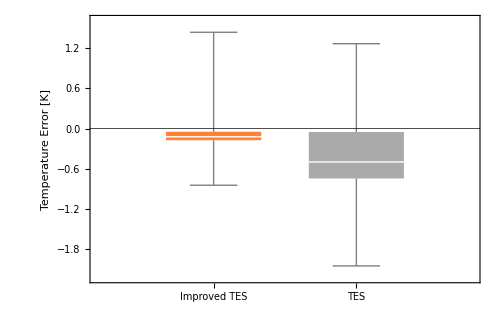

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerLowMMDSamplesForASTER],Flatten[TESTempErrorPerLowMMDSamplesForASTER]},
ChartStyle->{ASTERColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerLowMMDSamplesForASTER]]
Variance[Flatten[TESTempErrorPerLowMMDSamplesForASTER]]
```

0.0640574

0.248355

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForASTER]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForASTER]]
```

0.253096

0.498352

#### Temperature Error per high MMD

```mathematica
MMDThresholdForASTER=0.021;
highMMDPositions=Flatten[Position[trueEmisMMDASTER,_?(#>MMDThresholdForASTER&)]];
SBWTempErrorPerHighMMDSamplesForASTER=Table[SBWASTERTemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
TESTempErrorPerHighMMDSamplesForASTER=Table[TESASTERTemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
```

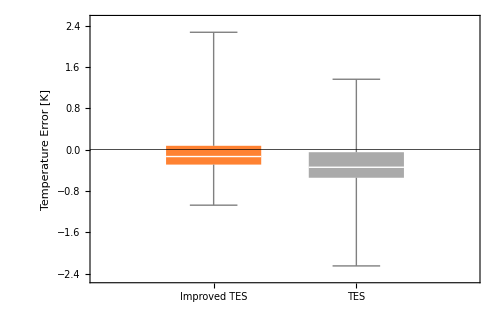

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerHighMMDSamplesForASTER],Flatten[TESTempErrorPerHighMMDSamplesForASTER]},
ChartStyle->{ASTERColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerHighMMDSamplesForASTER]]
Variance[Flatten[TESTempErrorPerHighMMDSamplesForASTER]]
```

0.126954

0.180923

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForASTER]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForASTER]]
```

0.356306

0.42535

#### Comparison

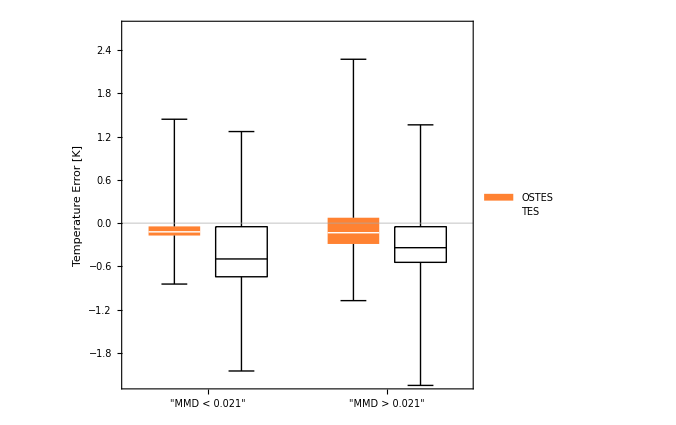

```mathematica
padding={{80,50},{40,40}};
TemperatureErrorPerMMDASTER=Show[
BoxWhiskerChart[
{{Flatten[SBWTempErrorPerLowMMDSamplesForASTER],None},{Flatten[SBWTempErrorPerHighMMDSamplesForASTER],None}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",White}},
ChartStyle->{{ASTERColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.021","MMD > 0.021"},{None}},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"ASTER"}},
BarSpacing->{0.3,0.9},
PlotRange->{-2.2,2.7},
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black,
ChartLegends->Placed[{"OSTES","TES"},{{0.07,0.73},{0,0}}]
],
BoxWhiskerChart[
{{None,Flatten[TESTempErrorPerLowMMDSamplesForASTER]},{None,Flatten[TESTempErrorPerHighMMDSamplesForASTER]}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",Black}},
ChartStyle->{{ASTERColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.021","MMD > 0.021"},{None}},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"ASTER"}},
BarSpacing->{0.3,0.9},
PlotRange->All,
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black
],
ImagePadding->padding
]
```

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForASTER]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForASTER]]
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForASTER]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForASTER]]
```

0.253096

0.498352

0.356306

0.42535

### AHS Temperature Error per MMD

```mathematica
samplesAHS=TrueEmisAHS[[samplesPosition,;;]];
trueEmisMMDAHS=Table[Max[samplesAHS[[i,;;]]]-Min[samplesAHS[[i,;;]]],{i,1,108}];
```

```mathematica
SBWTESTemperatureErrorPerSampleAHS=Table[SBWAHSTemp[[(i-1) 61+1;;i 61]],{i,1,108}];
TESTemperatureErrorPerSampleAHS=Table[TESAHSTemp[[(i-1) 61+1;;i 61]],{i,1,108}];
```

```mathematica
MMDThresholdForAHS=0.052;
```

#### Temperature error per low MMD

```mathematica
lowMMDPositions=Flatten[Position[trueEmisMMDAHS,_?(#<MMDThresholdForAHS&)]];
SBWTempErrorPerLowMMDSamplesForAHS=Table[SBWAHSTemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
TESTempErrorPerLowMMDSamplesForAHS=Table[TESAHSTemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
```

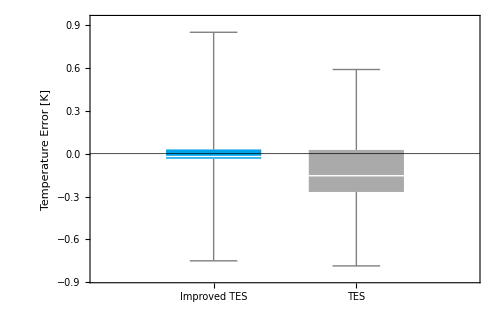

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerLowMMDSamplesForAHS],Flatten[TESTempErrorPerLowMMDSamplesForAHS]},
ChartStyle->{AHSColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerLowMMDSamplesForAHS]]
Variance[Flatten[TESTempErrorPerLowMMDSamplesForAHS]]
```

0.0175944

0.0381222

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForAHS]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForAHS]]
```

0.132644

0.195249

#### Temperature Error per high MMD

```mathematica
MMDThresholdForAHS=0.021;
highMMDPositions=Flatten[Position[trueEmisMMDAHS,_?(#>MMDThresholdForAHS&)]];
SBWTempErrorPerHighMMDSamplesForAHS=Table[SBWAHSTemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
TESTempErrorPerHighMMDSamplesForAHS=Table[TESAHSTemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
```

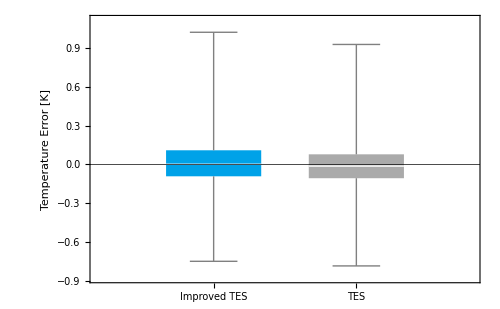

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerHighMMDSamplesForAHS],Flatten[TESTempErrorPerHighMMDSamplesForAHS]},
ChartStyle->{AHSColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerHighMMDSamplesForAHS]]
Variance[Flatten[TESTempErrorPerHighMMDSamplesForAHS]]
```

0.0391391

0.0369161

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForAHS]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForAHS]]
```

0.197836

0.192136

#### Comparison

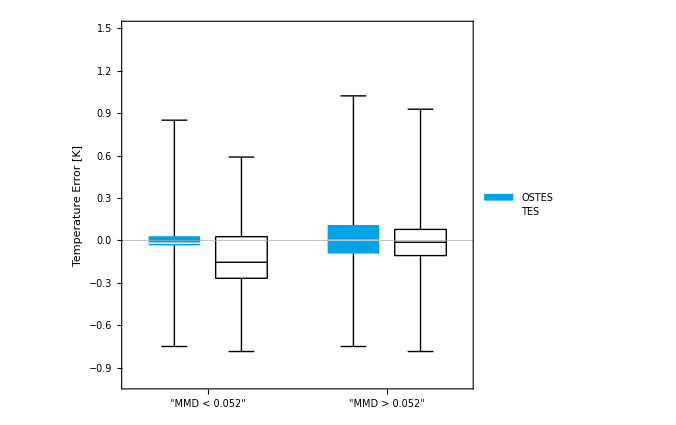

```mathematica
TemperatureErrorPerMMDAHS=Show[
BoxWhiskerChart[
{{Flatten[SBWTempErrorPerLowMMDSamplesForAHS],None},{Flatten[SBWTempErrorPerHighMMDSamplesForAHS],None}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",White}},
ChartStyle->{{AHSColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.052","MMD > 0.052"},{None}(*,{"Improved TES","TES"}*)},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"AHS"}},
BarSpacing->{0.3,0.9},
PlotRange->{-1.0,1.5},
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black,
ChartLegends->Placed[{"OSTES","TES"},{{0.07,0.73},{0,0}}]
],
BoxWhiskerChart[
{{None,Flatten[TESTempErrorPerLowMMDSamplesForAHS]},{None,Flatten[TESTempErrorPerHighMMDSamplesForAHS]}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",Black}},
ChartStyle->{{AHSColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.052","MMD > 0.052"},{None}(*,{"Improved TES","TES"}*)},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"AHS"}},
BarSpacing->{0.3,0.9},
PlotRange->All,
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black
],
ImagePadding->padding
]
```

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForAHS]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForAHS]]
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForAHS]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForAHS]]
```

0.132644

0.195249

0.197836

0.192136

### TASI Temperature Error per MMD

```mathematica
samplesTASI=TrueEmisTASI[[samplesPosition,;;]];
trueEmisMMDTASI=Table[Max[samplesTASI[[i,;;]]]-Min[samplesTASI[[i,;;]]],{i,1,108}];
```

```mathematica
SBWTESTemperatureErrorPerSampleTASI=Table[SBWTASITemp[[(i-1) 61+1;;i 61]],{i,1,108}];
TESTemperatureErrorPerSampleTASI=Table[TESTASITemp[[(i-1) 61+1;;i 61]],{i,1,108}];
```

```mathematica
MMDThresholdForTASI=0.026;
```

#### Temperature error per low MMD

```mathematica
lowMMDPositions=Flatten[Position[trueEmisMMDTASI,_?(#<MMDThresholdForTASI&)]];
SBWTempErrorPerLowMMDSamplesForTASI=Table[SBWTASITemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
TESTempErrorPerLowMMDSamplesForTASI=Table[TESTASITemp[[(i-1) 61+1;;i 61]],{i,lowMMDPositions}];
```

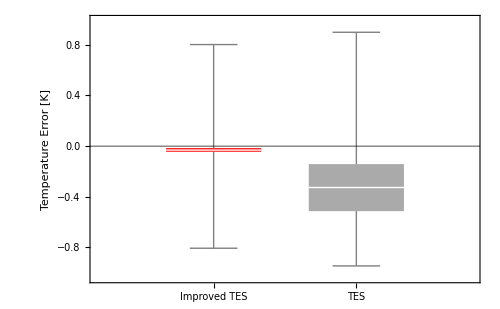

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerLowMMDSamplesForTASI],Flatten[TESTempErrorPerLowMMDSamplesForTASI]},
ChartStyle->{TASIColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerLowMMDSamplesForTASI]]
Variance[Flatten[TESTempErrorPerLowMMDSamplesForTASI]]
```

0.0255246

0.100754

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForTASI]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForTASI]]
```

0.159764

0.317418

#### Temperature Error per high MMD

```mathematica
MMDThresholdForTASI=0.021;
highMMDPositions=Flatten[Position[trueEmisMMDTASI,_?(#>MMDThresholdForTASI&)]];
SBWTempErrorPerHighMMDSamplesForTASI=Table[SBWTASITemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
TESTempErrorPerHighMMDSamplesForTASI=Table[TESTASITemp[[(i-1) 61+1;;i 61]],{i,highMMDPositions}];
```

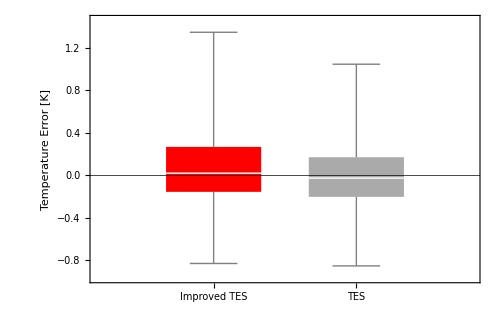

```mathematica
BoxWhiskerChart[
{Flatten[SBWTempErrorPerHighMMDSamplesForTASI],Flatten[TESTempErrorPerHighMMDSamplesForTASI]},
ChartStyle->{TASIColor,Lighter[Gray]},
ChartLabels->{"Improved TES","TES"},
GridLines->{None,{0}},
GridLinesStyle->Directive[Black],
BarOrigin->Bottom,
FrameLabel->{None,"Temperature Error [K]"},
BarSpacing->{0.5,0},
PlotRange->All,
ImageSize->500,
LabelStyle->{FontSize->22,FontFamily->font,Black}
]
```

```mathematica
Variance[Flatten[SBWTempErrorPerHighMMDSamplesForTASI]]
Variance[Flatten[TESTempErrorPerHighMMDSamplesForTASI]]
```

0.0996378

0.0902248

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForTASI]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForTASI]]
```

0.315655

0.300374

#### Comparison

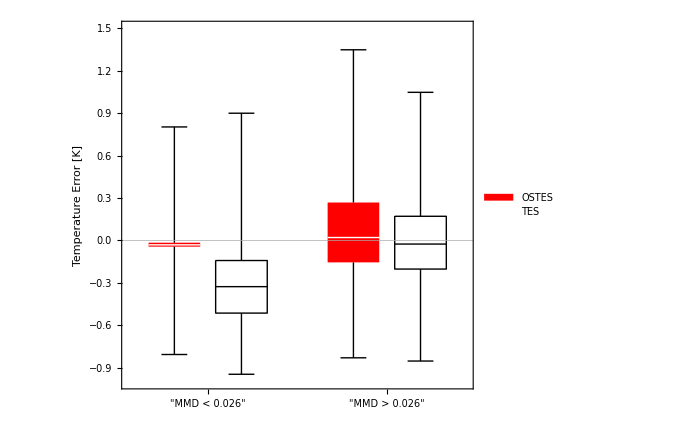

```mathematica
TemperatureErrorPerMMDTASI=Show[
BoxWhiskerChart[
{{Flatten[SBWTempErrorPerLowMMDSamplesForTASI],None},{Flatten[SBWTempErrorPerHighMMDSamplesForTASI],None}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",White}},
ChartStyle->{{TASIColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.026","MMD > 0.026"},{None}(*,{"Improved TES","TES"}*)},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"TASI"}},
BarSpacing->{0.3,0.9},
PlotRange->{-1.0,1.5},
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black,
ChartLegends->Placed[{"OSTES","TES"},{{0.07,0.73},{0,0}}]
],
BoxWhiskerChart[
{{None,Flatten[TESTempErrorPerLowMMDSamplesForTASI]},{None,Flatten[TESTempErrorPerHighMMDSamplesForTASI]}},
{{"Whiskers",Directive[Black,Thickness[0.002]]},{"Fences",Directive[Black,Thickness[0.002]]},{"MedianMarker",Black}},
ChartStyle->{{TASIColor,Directive[EdgeForm[{Black,Thickness[0.002]}],White]}},
ChartLabels->{{"MMD < 0.026","MMD > 0.026"},{None}(*,{"Improved TES","TES"}*)},
GridLines->{None,{0}},
GridLinesStyle->Lighter[Gray],
AspectRatio->0.85,
BarOrigin->Bottom,
FrameLabel->{{"Temperature Error [K]",None},{None,"TASI"}},
BarSpacing->{0.3,0.9},
PlotRange->All,
ImageSize->500,
GridLinesStyle->Directive[Black],
LabelStyle->{FontSize->fontSize+2,FontFamily->font,Black},
FrameStyle->Black
],
ImagePadding->padding
]
```

```mathematica
StandardDeviation[Flatten[SBWTempErrorPerLowMMDSamplesForTASI]]
StandardDeviation[Flatten[TESTempErrorPerLowMMDSamplesForTASI]]
StandardDeviation[Flatten[SBWTempErrorPerHighMMDSamplesForTASI]]
StandardDeviation[Flatten[TESTempErrorPerHighMMDSamplesForTASI]]
```

0.159764

0.317418

0.315655

0.300374

### Temperature Error per MMD - all in one row

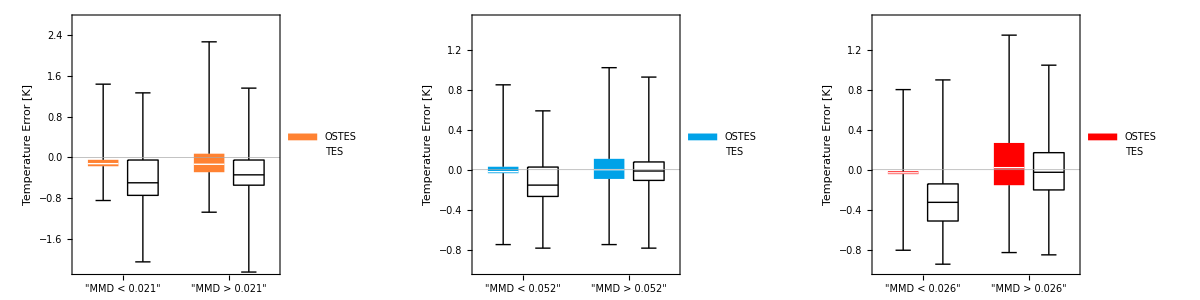

```mathematica
TableForm[
{{TemperatureErrorPerMMDASTER,TemperatureErrorPerMMDAHS,TemperatureErrorPerMMDTASI}},
TableSpacing->{0,7}
]
```